```mathematica
Clear["Global`*"]
```

# Bayesian Model of distance perception from ocular convergence

## Peter Scarfe and Paul Hibbard (2025)

## Code derives the distance prior consistent with a flat vergence prior

## We assume a flat prior for vergence for the reasons stated in the paper. But it is interesting to see what distance prior would be equivalent to a flat vergence prior. We use the same change of variables method to work this out.

```mathematica
(* Inverse transformation *)
xOfY=ArcTan[h/y];

(* Differentiate and that the absolute value*)
dxdy=Assuming[{h>0,y>0},FullSimplify[D[xOfY,y]]];
absDxDy=Assuming[{h>0,y∈Reals},FullSimplify[Abs[dxdy]]];

(* We define a uniform PDF *)
fX[x_]:=PDF[UniformDistribution[{a,b}],x];

(* Change of variable with the assumptions we can make with the physical geometry *)
theAssumptions={h>0,y>0,0<a<b<Pi/2,a<=ArcTan[h/y]<=b};
fY[y_]:=FullSimplify[fX[xOfY]*absDxDy,Assumptions->theAssumptions];
fY[y]
```

h/((-a+b) (h^2+y^2))

```mathematica
(* Substitute in the domain of vergence and show that this integrates to 1 as expected *)
fyToInt=fY[y]/. {a->0,b->Pi/2};
Integrate[PDF[ProbabilityDistribution[fyToInt,{y,0,Infinity}],y],{y,0,Infinity},Assumptions->h>0]
```

1

```mathematica
(* Substitute and plot the PDF *)
pdfForPlotting=fY[y]/. {a->0,b->Pi/2,h->3.25};
distPlot=Plot[PDF[ProbabilityDistribution[pdfForPlotting,{y,0,Infinity}],y],{y,0,100},PlotRange->All];
```

```mathematica
(* For comparison and a sanity check to the same but Monte Carlo *)
vergs=RandomVariate[UniformDistribution[{0,Pi/2}],100000];
dists = 3.25/Tan[vergs];
distHist=Histogram[dists,{0,100,1},"PDF",Frame->True,FrameLabel->{"Distance (cm)","Probability"},BaseStyle->14,ImageSize->Large,PlotLabel->"Distance Prior consistent with a flat vergence prior"];
```

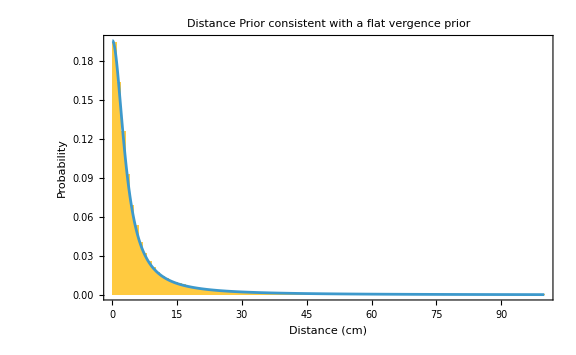

```mathematica
(* Plot *)
Show[{distHist,distPlot}]
```

For the paper we have plotted all of the priors in DataGraph. Therefore to maintain consistent formatting we export the evaluated PDFs for plotting in DataGraph.

```mathematica
(* First for Distance *)
numSteps=500;
f[y_]=pdfForPlotting;
fineX=Range[0,100,100/numSteps];
fineY=f[fineX];
data=Transpose[{fineX,fineY}];
```

```mathematica
(* Then for vergence *)
xVerg=Range[0,Pi/2,(Pi/2)/numSteps]//N;
fv[x_]=PDF[UniformDistribution[{0,Pi/2}],x];
fvSimp[x_]=FullSimplify[fv[x],0<x<Pi/2];
fineVergY=fvSimp/@xVerg//N;
dataVerg=Transpose[{xVerg,fineVergY}];
```

```mathematica
Export[NotebookDirectory[]<>"distVergFlat.txt",Join[data,dataVerg,2],"Table"];
```